```mathematica
Quit[]
Exit[]
```

```mathematica
Get["/home/claire/policingdemography/policingdemography/policingdemography.wl"]
```

```mathematica
myGrayScale={{"myGrayScale","",{}},{"Gradients"},1,{0,1},{LightGray,White},""};
AppendTo[DataPaclets`ColorDataDump`colorSchemes,myGrayScale];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,myGrayScale[[1,1]]];
ColorData["myGrayScale"]
```

ColorDataFunction[…]

## Selection gradient and other useful functions of the model

```mathematica
sel=((1-m) (-1+m) n^4 rb^2 (n (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)+Bb (-n (-1+p) y)^γ (-2+γ)) (C1 n y+2 C2 n y^2-n Pp y (p y)^η-Bb (-n (-1+p) y)^γ γ+n Pp (p y)^η η-n Pp y (p y)^η η))/((1+2 m (-1+n)-m^2 (-1+n)) y (n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))^4 (1-((-1+m)^2 rb (Bb^2 rb th (-n (-1+p) y)^(2 γ)-2 Bb n rb th (-n (-1+p) y)^γ (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)+n^2 (rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)^2+Bb (-n (-1+p) y)^γ (-1+γ))))/((n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))^2)))-(n^2 rb (C1 (-1-2 m (-1+n)+m^2 (-1+n)) n y+2 C2 (-1-2 m (-1+n)+m^2 (-1+n)) n y^2+n Pp y (p y)^η-2 m n Pp y (p y)^η+m^2 n Pp y (p y)^η+2 m n^2 Pp y (p y)^η-m^2 n^2 Pp y (p y)^η+Bb (-n (-1+p) y)^γ γ-n Pp (p y)^η η+n Pp y (p y)^η η))/((-1-2 m (-1+n)+m^2 (-1+n)) y (n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))^2);
F[xm_,n_,nr_]:=(1-m)w[xm,xm,n]n+m nr;
w[x_,xn_,n_]:=re[x,xn,n]/(1+th re[x,xn,n]);
re[x_,xn_,n_]:=rb/n(1-(x C1+x^2 C2)+Bb((x+(n-1)xn)(1-p))^γ/n-Pp(1-x)((x+(n-1)xn)/n p)^η);
monopop={x->y,xn->y,xm->y,nr->n,r->(1-m)^2/(1+(1-(1-m)^2)(n-1)),r̄->1/n+(1-1/n)r};
```

```mathematica
sel/.{γ->1,η->1}//Simplify
```

(n rb (((C1+2 C1 m (-1+n)-C1 m^2 (-1+n)+Bb (-1+p)+p Pp+2 C2 y-4 C2 m y+2 C2 m^2 y+4 C2 m n y-2 C2 m^2 n y-2 p Pp y+2 m p Pp y-m^2 p Pp y-2 m n p Pp y+m^2 n p Pp y) (n-rb th (-1+C1 y+Bb (-1+p) y+p Pp y+C2 y^2-p Pp y^2))^2)/(-1-2 m (-1+n)+m^2 (-1+n))+((1-m) (-1+m) n rb (C1+Bb (-1+p)+p Pp+2 C2 y-2 p Pp y) (-1+C1 y+Bb (-1+p) y+p Pp y+C2 y^2-p Pp y^2))/((1+2 m (-1+n)-m^2 (-1+n)) (1-((-1+m)^2 rb^2 th (-1+C1 y+Bb (-1+p) y+p Pp y+C2 y^2-p Pp y^2)^2)/((n-rb th (-1+C1 y+Bb (-1+p) y+p Pp y+C2 y^2-p Pp y^2))^2)))))/(n-rb th (-1+C1 y+Bb (-1+p) y+p Pp y+C2 y^2-p Pp y^2))^4

## Explore parameters

```mathematica
(*pars={th->0.1,rb->20,c1->0,c2->0.1,b->2,d->0.3,p->0.5,eta->1,gamma->1,m->0.5};*)
```

Generate an error message

```mathematica
search[{{0.1},Range[1,3,2],{0},{0.1},{2},{0.3},{0.5},{1},{1}}]
```

search::len: You gave 9 parameters, this model needs 10

### Launch a browse

```mathematica
(*Parameters order: th,rb,c1,c2,b,d,p,eta,gamma,m*)
```

```mathematica
thRange=Range[0.05,0.2,0.05];
rbRange=Range[1,50,5];
c1Range=Range[0,2,0.5];
c2Range=Range[0,2,0.5];
bRange=Range[1,50,5];
dRange=Range[0.5,10,2];
pRange=Range[0.2,0.8,0.2];
etaRange=Range[0.5,2,0.5];
gammaRange=Range[2,6,1];
mRange=Range[0.2,0.8,0.2];
```

```mathematica
saveTest=search[{thRange,rbRange,c1Range,c2Range,bRange,dRange,pRange,etaRange,gammaRange,mRange}];
```

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^4 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Divide::infy: Infinite expression 1/0. encountered.

$Aborted[]

Divide::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

$Aborted[]

GroebnerBasis`DistributedTermsList::fltgb: Excessive loss of precision during computation.

General::stop: Further output of GroebnerBasis`DistributedTermsList::fltgb will be suppressed during this calculation.

$Aborted[]

SetPrecision::precsm: Requested precision -93.2041 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of SetPrecision::precsm will be suppressed during this calculation.

General::munfl: (-1.08717×10^17-1.88303×10^17 ⅈ)^6 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted[]

ReplaceAll::reps: {Removed[$$Failure]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Export["/home/claire/Dropbox/PhD/Data/Analyses/parameter_exploration.m",saveTest]
```

/home/claire/Dropbox/PhD/Data/Analyses/parameter_exploration.m

### Checking where we have the results of interest

We want sZero=S(y=0,n=n*(y=1)) <0, sEqui[[1]] =S(y=0,n=n*(y=0))>0, nZero=n*(y=0)<<nOne=n*(y=1)

```mathematica
data=Import["/home/claire/Dropbox/PhD/Data/Analyses/parameter_exploration.m"];
```

```mathematica
AllTrue[data[["res",1, "sEqui",1;;6]],Positive](*sEqui is S(y,n^*(y)) for y={~0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}*)
```

True

```mathematica
AllTrue[{True,False}]
```

AllTrue[{True,False}]

Find position of parameter set for which each criteria is met independently

```mathematica
smallNZero=Position[data[["res",All,"nZero"]],_?(#<30&),1];
largeNOne=Position[data[["res",All,"nOne"]],_?(#>150&),1];
negativeSZero=Position[data[["res",All,"sZero"]],_?Negative];
positiveSOne=Position[data[["res",All,"sEqui",1]],_?Positive];
mostlyPositiveGradient=DeleteCases[Table[If[AllTrue[data[["res",i, "sEqui",1;;2]],Positive],i,None],{i,Length[data[["res"]]]}],None];
Length[#]&/@{smallNZero,largeNOne,negativeSZero,positiveSOne,mostlyPositiveGradient}
```

{145000,90715,131170,89975,45516}

Find positions of parameter sets fulfilling all criteria at once

```mathematica
Mean[data[["res",#,"nOne"]]&/@mostlyPositiveGradient]
```

157.363

```mathematica
Max[data[["res",#,"nZero"]]&/@mostlyPositiveGradient]
```

43.7

```mathematica
pos=Flatten[Intersection[smallNZero,largeNOne,mostlyPositiveGradient]];
Length[pos]
```

0

```mathematica
colorPar[parRange_,parPos_]:=Block[{},
If[MemberQ[DeleteDuplicates[data[["comb",pos,parPos]]],#],Style[#,Darker[Green],20],#]&/@parRange]
```

```mathematica
{"T_h",colorPar[thRange,1]}
{"r_b",colorPar[rbRange,2]}
{"c_1",colorPar[c1Range,3]}
{"c_2",colorPar[c2Range,4]}
{"b",colorPar[bRange,5]}
{"d",colorPar[dRange,6]}
{"p",colorPar[pRange,7]}
```

{T_h,{0.05,0.1,0.15,0.2}}

{r_b,{1,6,11,16,21,26,31,36,41,46}}

{c_1,{0.,0.5,1.,1.5,2.}}

{c_2,{0.,0.5,1.,1.5,2.}}

{b,{1,6,11,16,21,26,31,36,41,46}}

{d,{0.5,2.5,4.5,6.5,8.5}}

{p,{0.2,0.4,0.6,0.8}}

```mathematica
thFixed=0.1;
rbFixed=16;
c1Fixed=1.5;
c2Fixed=2;
bFixed=36;
dFixed=4.5;
pFixed=0.2;
thFixedPos=Flatten[Position[data[[1,All,1]],thFixed]];
rbFixedPos=Flatten[Position[data[[1,All,2]],rbFixed]];
c1FixedPos=Flatten[Position[data[[1,All,3]],c1Fixed]];
c2FixedPos=Flatten[Position[data[[1,All,4]],c2Fixed]];
bFixedPos=Flatten[Position[data[[1,All,5]],bFixed]];
dFixedPos=Flatten[Position[data[[1,All,6]],dFixed]];
pFixedPos=Flatten[Position[data[[1,All,7]],pFixed]];
```

#### Looking at c_2 and b more specifically

```mathematica
plotc2VSb[c1val_]:=Block[{c2VSb,plotRes},
c2VSb=search[{{0.1},{16},{c1val},Range[1,50,0.2],Range[1,50,0.2],{4.5},{0.2},{2},{1},{0.2}}];
Export[ToString[StringForm["/home/claire/Dropbox/PhD/Data/Analyses/parameter_exploration_bVSc2_c1=``.m",c1val]],c2VSb];
plotRes=Row[{ListContourPlot[{c2VSb[["comb"]][[#,4]],c2VSb[["comb"]][[#,5]],Sign[c2VSb[["res"]][[#,"sZero"]]]}&/@Range[Length[c2VSb[["res"]]]],Contours->1,ColorFunction->ColorData["myGrayScale"],FrameLabel->(Style[#,20]&/@{"Quadratic investment costs, c_2","Direct returns on investment, b","S(y≃0,n̂(y=1))"}),Frame->True,ImageSize->500],
ListContourPlot[{c2VSb[["comb"]][[#,4]],c2VSb[["comb"]][[#,5]],Sign[c2VSb[["res"]][[#,"sEqui",1]]]}&/@Range[Length[c2VSb[["res"]]]],PlotLegends->Automatic,Contours->1,ColorFunction->ColorData["myGrayScale"],FrameLabel->(Style[#,20]&/@{"Quadratic investment costs, c_2","","S(y≃0,n̂(y≃0))"}),Frame->True,ImageSize->500],
ListDensityPlot[{c2VSb[["comb"]][[#,4]],c2VSb[["comb"]][[#,5]],c2VSb[["res"]][[#,"nZero"]]}&/@Range[Length[c2VSb[["res"]]]],ColorFunction->ColorData["BlueGreenYellow"],FrameLabel->(Style[#,20]&/@{"Quadratic investment costs, c_2","","n̂(y≃0)"}),Frame->True,ImageSize->500,PlotLegends->Automatic],
Show[{ListDensityPlot[{c2VSb[["comb"]][[#,4]],c2VSb[["comb"]][[#,5]],c2VSb[["res"]][[#,"nOne"]]}&/@Range[Length[c2VSb[["res"]]]],PlotLegends->Automatic,ColorFunction->ColorData["BlueGreenYellow"],FrameLabel->(Style[#,20]&/@{"Quadratic investment costs, c_2","","n̂(y≃1)"}),Frame->True,ImageSize->500],ListContourPlot[{c2VSb[["comb"]][[#,4]],c2VSb[["comb"]][[#,5]],c2VSb[["res"]][[#,"nOne"]]}&/@Range[Length[c2VSb[["res"]]]],Contours->{0},ContourShading->None,FrameLabel->(Style[#,20]&/@{"Quadratic investment costs, c_2","","n̂(y≃1)"}),Frame->True,ImageSize->500]}]}];
Export[ToString[StringForm["/home/claire/Dropbox/PhD/Results/figs/anal_sn_bc2_c1=``.png",c1val]],plotRes];
Print["Graph exported"]]
```

```mathematica
plotc2VSb[#]&/@{0,0.5,1,1.5,2,2.5,3,3.5,4,10,20,30,40,50}
```

Power::infy: Infinite expression 1/0.^4 encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

#### Plotting results for varying d and c1

```mathematica
plotc1VSd[pval_]:=Block[{c1VSd,plotRes},
c1VSd=search[{{0.1},{16},Range[1,50,0.2],{5},{45},Range[1,50,0.2],{pval},{2},{1},{0.2}}];
Export[ToString[StringForm["/home/claire/Dropbox/PhD/Data/Analyses/parameter_exploration_c1VSd_p=``.m",pval]],c1VSd];
plotRes=Row[{ListContourPlot[{c1VSd[["comb"]][[#,3]],c1VSd[["comb"]][[#,6]],Sign[c1VSd[["res"]][[#,"sZero"]]]}&/@Range[Length[c1VSd[["res"]]]],Contours->1,ColorFunction->ColorData["myGrayScale"],FrameLabel->(Style[#,20]&/@{"Quadratic investment costs, c_2","Direct returns on investment, b","S(y≃0,n̂(y=1))"}),Frame->True,ImageSize->500],
ListContourPlot[{c1VSd[["comb"]][[#,3]],c1VSd[["comb"]][[#,6]],Sign[c1VSd[["res"]][[#,"sEqui",1]]]}&/@Range[Length[c1VSd[["res"]]]],PlotLegends->Automatic,Contours->1,ColorFunction->ColorData["myGrayScale"],FrameLabel->(Style[#,20]&/@{"Quadratic investment costs, c_2","","S(y≃0,n̂(y≃0))"}),Frame->True,ImageSize->500],
ListDensityPlot[{c1VSd[["comb"]][[#,3]],c1VSd[["comb"]][[#,6]],c1VSd[["res"]][[#,"nZero"]]}&/@Range[Length[c1VSd[["res"]]]],ColorFunction->ColorData["BlueGreenYellow"],FrameLabel->(Style[#,20]&/@{"Quadratic investment costs, c_2","","n̂(y≃0)"}),Frame->True,ImageSize->500,PlotLegends->Automatic],
Show[{ListDensityPlot[{c1VSd[["comb"]][[#,3]],c1VSd[["comb"]][[#,6]],c1VSd[["res"]][[#,"nOne"]]}&/@Range[Length[c1VSd[["res"]]]],PlotLegends->Automatic,ColorFunction->ColorData["BlueGreenYellow"],FrameLabel->(Style[#,20]&/@{"Quadratic investment costs, c_2","","n̂(y≃1)"}),Frame->True,ImageSize->500],ListContourPlot[{c1VSd[["comb"]][[#,3]],c1VSd[["comb"]][[#,6]],c1VSd[["res"]][[#,"nOne"]]}&/@Range[Length[c1VSd[["res"]]]],Contours->{0},ContourShading->None,FrameLabel->(Style[#,20]&/@{"Quadratic investment costs, c_2","","n̂(y≃1)"}),Frame->True,ImageSize->500]}]}];
Export[ToString[StringForm["/home/claire/Dropbox/PhD/Results/figs/anal_sn_dc1_p=``.png",pval]],plotRes];
Print["Graph exported"]]
```

```mathematica
c1VSd=Import["/home/claire/Dropbox/PhD/Data/Analyses/parameter_exploration_c1VSd_p=0.1.m"]
```

<|comb→{{0.1,16,1.,5,45,1.,0.1,2,1,0.2},{0.1,16,1.,5,45,1.2,0.1,2,1,0.2},{0.1,16,1.,5,45,1.4,0.1,2,1,0.2},{0.1,16,1.,5,45,1.6,0.1,2,1,0.2},{0.1,16,1.,5,45,1.8,0.1,2,1,0.2},60506,{0.1,16,50.,5,45,49.2,0.1,2,1,0.2},{0.1,16,50.,5,45,49.4,0.1,2,1,0.2},{0.1,16,50.,5,45,49.6,0.1,2,1,0.2},{0.1,16,50.,5,45,49.8,0.1,2,1,0.2},{0.1,16,50.,5,45,50.,0.1,2,1,0.2}},res→{1}|>
 |  |  |  |

```mathematica
Sign[c1VSd[["res"]][[All,"sZero"]]]
```

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,60324,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}
 |  |  |  |

```mathematica
plotc1VSdImportData[pval_]:=Block[{c1VSd,plotRes},
c1VSd=Import[ToString[StringForm["/home/claire/Dropbox/PhD/Data/Analyses/parameter_exploration_c1VSd_p=``.m",pval]]];
plotRes=Row[{ListContourPlot[{c1VSd[["comb"]][[#,3]],c1VSd[["comb"]][[#,6]],Sign[c1VSd[["res"]][[#,"sZero"]]]}&/@Range[Length[c1VSd[["res"]]]],Contours->1,ColorFunction->ColorData["myGrayScale"],FrameLabel->(Style[#,20]&/@{"Quadratic investment costs, c_2","Direct returns on investment, b","S(y≃0,n̂(y=1))"}),Frame->True,ImageSize->500],
ListContourPlot[{c1VSd[["comb"]][[#,3]],c1VSd[["comb"]][[#,6]],Sign[c1VSd[["res"]][[#,"sEqui",1]]]}&/@Range[Length[c1VSd[["res"]]]],PlotLegends->Automatic,Contours->1,ColorFunction->ColorData["myGrayScale"],FrameLabel->(Style[#,20]&/@{"Quadratic investment costs, c_2","","S(y≃0,n̂(y≃0))"}),Frame->True,ImageSize->500],
ListDensityPlot[{c1VSd[["comb"]][[#,3]],c1VSd[["comb"]][[#,6]],c1VSd[["res"]][[#,"nZero"]]}&/@Range[Length[c1VSd[["res"]]]],ColorFunction->ColorData["BlueGreenYellow"],FrameLabel->(Style[#,20]&/@{"Quadratic investment costs, c_2","","n̂(y≃0)"}),Frame->True,ImageSize->500,PlotLegends->Automatic],
Show[{ListDensityPlot[{c1VSd[["comb"]][[#,3]],c1VSd[["comb"]][[#,6]],c1VSd[["res"]][[#,"nOne"]]}&/@Range[Length[c1VSd[["res"]]]],PlotLegends->Automatic,ColorFunction->ColorData["BlueGreenYellow"],FrameLabel->(Style[#,20]&/@{"Quadratic investment costs, c_2","","n̂(y≃1)"}),Frame->True,ImageSize->500],ListContourPlot[{c1VSd[["comb"]][[#,3]],c1VSd[["comb"]][[#,6]],c1VSd[["res"]][[#,"nOne"]]}&/@Range[Length[c1VSd[["res"]]]],Contours->{0},ContourShading->None,FrameLabel->(Style[#,20]&/@{"Quadratic investment costs, c_2","","n̂(y≃1)"}),Frame->True,ImageSize->500]}]}];
Export[ToString[StringForm["/home/claire/Dropbox/PhD/Results/figs/anal_sn_dc1_p=``.png",pval]],plotRes];
Print["Graph exported"]]
```

```mathematica
plotc1VSdImportData[#]&/@Range[0,1,0.1]
```

Graph exported

Graph exported

Graph exported

«8 more identical outputs»

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

#### Varying c1 and p

```mathematica
Length[Range[1,50,0.2]]
```

246

```mathematica
Length[Range[0,1,0.004]]
```

251

```mathematica
c1VSp=search[{{0.1},{16},Range[1,50,0.2],{5},{45},{20},Range[0,1,0.004],{2},{1},{0.2}}];
Export["/home/claire/Dropbox/PhD/Data/Analyses/parameter_exploration_c1VSp.m",c1VSp];
```

Power::infy: Infinite expression 1/0.^4 encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
c1VSp=Import["/home/claire/Dropbox/PhD/Data/Analyses/parameter_exploration_c1VSp.m"];
```

```mathematica
plotRes=Row[{ListContourPlot[{c1VSp[["comb"]][[#,3]],c1VSp[["comb"]][[#,7]],Sign[c1VSp[["res"]][[#,"sZero"]]]}&/@Range[Length[c1VSp[["res"]]]],Contours->1,ColorFunction->ColorData["myGrayScale"],FrameLabel->(Style[#,20]&/@{"Linear investment costs, c_1","Policing level, p","S(y≃0,n̂(y=1))"}),Frame->True,ImageSize->500],
ListContourPlot[{c1VSp[["comb"]][[#,3]],c1VSp[["comb"]][[#,7]],Sign[c1VSp[["res"]][[#,"sEqui",1]]]}&/@Range[Length[c1VSp[["res"]]]],PlotLegends->Automatic,Contours->1,ColorFunction->ColorData["myGrayScale"],FrameLabel->(Style[#,20]&/@{"Linear investment costs, c_1","","S(y≃0,n̂(y≃0))"}),Frame->True,ImageSize->500],
ListDensityPlot[{c1VSp[["comb"]][[#,3]],c1VSp[["comb"]][[#,7]],c1VSp[["res"]][[#,"nZero"]]}&/@Range[Length[c1VSp[["res"]]]],ColorFunction->ColorData["BlueGreenYellow"],FrameLabel->(Style[#,20]&/@{"Linear investment costs, c_1","","n̂(y≃0)"}),Frame->True,ImageSize->500,PlotLegends->Automatic],
Show[{ListDensityPlot[{c1VSp[["comb"]][[#,3]],c1VSp[["comb"]][[#,7]],c1VSp[["res"]][[#,"nOne"]]}&/@Range[Length[c1VSp[["res"]]]],PlotLegends->Automatic,ColorFunction->ColorData["BlueGreenYellow"],FrameLabel->(Style[#,20]&/@{"Linear investment costs, c_1","","n̂(y≃1)"}),Frame->True,ImageSize->500],ListContourPlot[{c1VSp[["comb"]][[#,3]],c1VSp[["comb"]][[#,7]],c1VSp[["res"]][[#,"nOne"]]}&/@Range[Length[c1VSp[["res"]]]],Contours->{0},ContourShading->None,FrameLabel->(Style[#,20]&/@{"Linear investment costs, c_1","","n̂(y≃1)"}),Frame->True,ImageSize->500]}]}]
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
Export["/home/claire/Dropbox/PhD/Results/figs/anal_sn_c1_p.png",plotRes]
```

/home/claire/Dropbox/PhD/Results/figs/anal_sn_c1_p.png

#### Plotting results for varying c_2 and b, other parameters fixed (see above for newer version)

Looking at the effect of c2 and b on s when y is near 0 and n is at the ecological equilibrium for y=1

```mathematica
linesOfInterest=Intersection[thFixedPos,rbFixedPos,c1FixedPos,dFixedPos,pFixedPos];
resval=data[[2,#,"sZero"]]&/@linesOfInterest;
c2val=data[[1,#,4]]&/@linesOfInterest;
bval=data[[1,#,5]]&/@linesOfInterest;
```

Effect of c2 and b on s when y is near 0 and n is at the ecological equilibrium for y = 1

```mathematica
resvalsEqui0=data[[2,#,"sEqui",1]]&/@linesOfInterest;
```

```mathematica
ColorData["GrayTones",Opacity[0.5]]
```

ColorData::notprop: Opacity[0.5] is not a known property for ColorData. Use ColorData["Properties"] for a list of properties.

ColorData[GrayTones,Opacity[0.5]]

```mathematica
Opacity[0.5,ColorData["GrayYellowTones"]]
```

Opacity[0.5,ColorDataFunction[…]]

```mathematica
ColorData[1];
new={{"play","",{}},{"Gradients"},1,{0,1},{Gray,LightGray},""};
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];
ColorData["play"]
```

ColorDataFunction[…]

```mathematica
new
```

{{play,,{}},{Gradients},1,{0,1},{GrayLevel[0.5],GrayLevel[0],GrayLevel[0.85]},}

```mathematica
LightGray
```

GrayLevel[0.85]

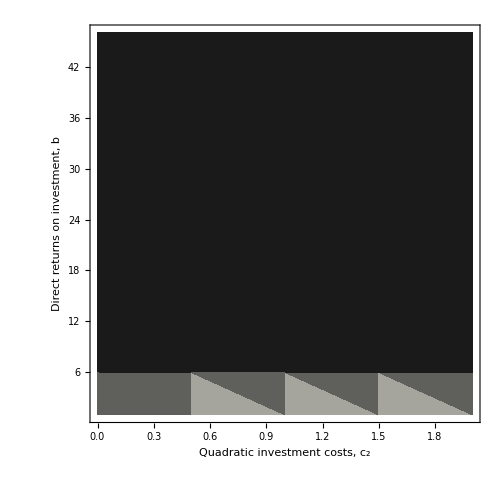
-Graphics--Graphics-

```mathematica
gradientPlot=Row[{ListDensityPlot[{c2val[[#]],bval[[#]],Sign[resval[[#]]]}&/@Range[Length[bval]],PlotRange->Full,ColorFunction->ColorData["GrayTones"],FrameLabel->(Style[#,20]&/@{"Quadratic investment costs, c_2","Direct returns on investment, b","S(y≃0,n̂(y=1))"}),Frame->True,ImageSize->500],ListDensityPlot[{c2val[[#]],bval[[#]],Sign[resvalsEqui0[[#]]]}&/@Range[Length[bval]],PlotLegends->Automatic,PlotRange->Full,ColorFunction->ColorData["play"],FrameLabel->(Style[#,20]&/@{"Quadratic investment costs, c_2","","S(y≃0,n=n̂(y=0))"}),Frame->True,ImageSize->500]}]
```

```mathematica
Export["/home/claire/Dropbox/PhD/Results/figs/anal_gradient_c2VSb_c1=1.5.png",gradientPlot]
```

/home/claire/Dropbox/PhD/Results/figs/anal_gradient_c2VSb_c1=1.5.png

effect on n at equilibrium when y is 1

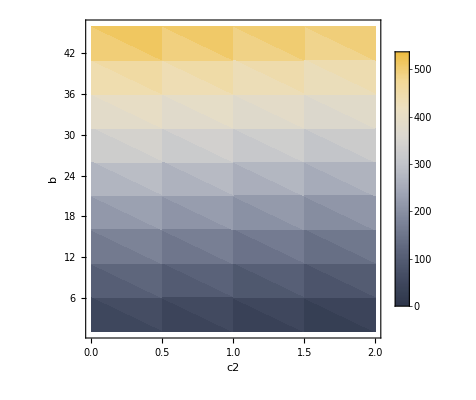

```mathematica
resvalnOne=data[[2,#,"nOne"]]&/@linesOfInterest;ListDensityPlot[{c2val[[#]],bval[[#]],resvalnOne[[#]]}&/@Range[Length[bval]],PlotLegends->Automatic,PlotRange->Full,ColorFunction->ColorData["GrayYellowTones"],FrameLabel->(Style[#,20]&/@{"c2","b","n^*(y=1)"}),Frame->True]
```